## Two Neutrino Probabilities in Vacuum

```mathematica
Clear["Global`*"]

(* Definitions *)
Norm2[z_]=Re[z]^2+Im[z]^2;
c12:=Cos[θ12];
s12:=Sin[θ12];
ots=1.2669327621645516 ; (*constant due to changing parameters *)

(* Experimental data of mixing parameter θ and masses diferrence Δms between flavors 1 and 2 *)
θ12=ArcSin[Sqrt[0.86]]/2;
Δms12=0.0000759;
```

```mathematica
(* Computing conversion probability (1 -> 2) or survival probability (1 -> 1) *)

P[α_,β_,LE_,θ12_,Δms12_]=
Block[{U,m1,m2},
m1=0;
m2=Δms12;

(* Pontecorvo–Maki–Nakagawa–Sakata matrix U *)
U[k_,j_]:=If[k==1,If[j==1, c12, If[j==2, s12]],If[k==2,If[j==1,- s12,If[j==2, c12]]]];
Norm2[Sum[Conjugate[U[α,i]] U[β,i] E^(-2 I ots If[i==1,m1,If[i==2,m2]] LE),{i,1,2}]]
];
```

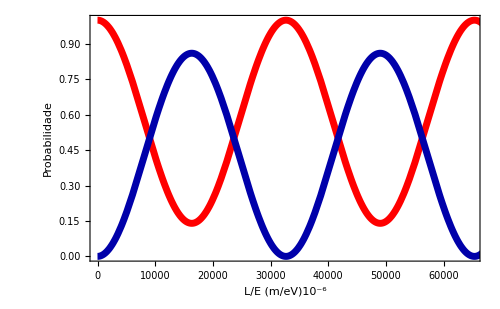

```mathematica
Plot[{P[1,1,LE,θ12,Δms12],P[1,2,LE,θ12,Δms12]},{LE,0,100000},PlotRange->{{0,65000},{0,1}},PlotStyle->{{Red,Thickness[0.01]},{Darker[Blue],Thickness[0.01]}},Frame->True,FrameLabel->{{"Probabilidade",""},{"L/E (m/eV)10^-6", "Oscilação para um Neutrino Eletrônico"}},
BaseStyle->{FontSize->14,Bold},ImageSize->500]
```